```mathematica
Блок приборов
```

```mathematica
Mn={10,30,57,55,103,120,140,158};
Mv={-15,-15,-14,-13,-12,-11,-10.5,-10};
Q={0.1422,0.1397,0.1334,0.1335,0.1220,0.1167,0.1056,0.0422};
n={60,59.8,59.7,59.7,59.6,59.2,59,59};
Md={0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4};
```

```mathematica
Обработка
```

```mathematica
Mnn=Mn*6/250.
```

{0.24,0.72,1.368,1.32,2.472,2.88,3.36,3.792}

```mathematica
Mvv=Mv*10^-3//N
```

{-0.015,-0.015,-0.014,-0.013,-0.012,-0.011,-0.0105,-0.01}

```mathematica
ph=Mnn-Mvv
```

{0.255,0.735,1.382,1.333,2.484,2.891,3.3705,3.802}

```mathematica
nn=n*3000/120
```

{1500,1495.,1492.5,1492.5,1490.,1480.,1475,1475}

```mathematica
Sum[nn[[i]],{i,1,Length[nn]}]/Length[nn]
```

1487.5

```mathematica
Npol=Table[ph[[i]]*Q[[i]]*10^3,{i,1,Length[ph]}]
```

{36.261,102.679,184.359,177.956,303.048,337.38,355.925,160.444}

```mathematica
Nd=Table[Md[[i]]*nn[[i]]*Pi/30*9.81,{i,1,Length[Md]}]
```

{77.0476,153.581,229.987,306.649,382.67,456.122,530.344,606.107}

```mathematica
heta=Table[100Npol[[i]]/Nd[[i]],{i,1,Length[n]}]
```

{47.0631,66.8567,80.1605,58.0323,79.1931,73.9671,67.1121,26.4713}

```mathematica
Vo=2Pi 12*10^-3((17.5*10^-3)^2-(15*10^-3)^2-(7.38*10^-3)^2/12)*10^3
```

0.0057839

```mathematica
Qi=Vo*nn/60
```

{0.144597,0.144115,0.143874,0.143874,0.143633,0.142669,0.142187,0.142187}

```mathematica
Kq=Table[ Q[[i]]/Qi[[i]] ,{i,1,Length[Q]}]
```

{0.98342,0.969362,0.927198,0.927893,0.849385,0.817975,0.742682,0.296791}

```mathematica
T1={Transpose@{ph,heta/100},     Transpose@{ph,Kq}       };
T2={Transpose@{ph,Q},Transpose@{ph,Nd}         };
```

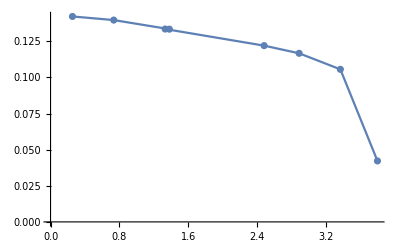

```mathematica
Show@{ListPlot[Transpose@{ph,Q}],ListLinePlot[Transpose@{ph,Q}]}
```

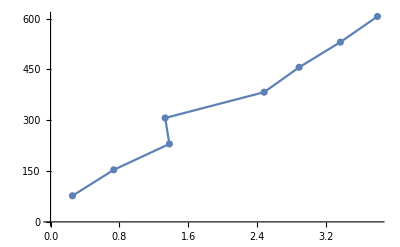

```mathematica
Show@{ListPlot[Transpose@{ph,Nd} ],ListLinePlot[Transpose@{ph,Nd} ]}
```

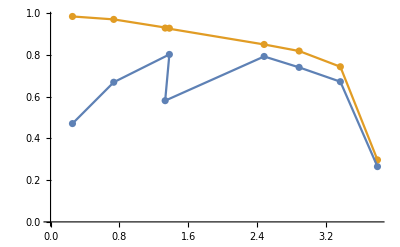

```mathematica
Show@{ListPlot[T1],ListLinePlot[T1]}
```